```mathematica
dist2[μ_,x0_,Ν_,n_]:=Abs[gn[μ,x0,Ν]-gn[μ,x0,Ν+2^n]]
indagine2[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist2[μ,x0,Ν,n]},{μ,min,max,step}]
indagine2Plot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine2[n,x0,Ν,{min,max,step}],]
sospetto2[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine2[n,x0,Ν,{min,max,step}]/.,
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevole2[n_,x0_,Ν_,{min_,max_,step_}]:=sospetto2[n,x0,Ν,{min,max,step}]⟦1,1⟧
```

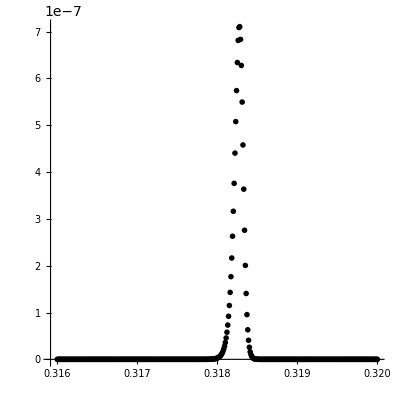

```mathematica
indagine2Plot[1,0.3,10^4,{0.316,0.32,10^-5}]
```

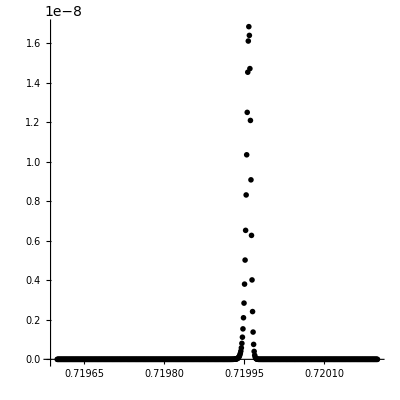

```mathematica
indagine2Plot[2,0.3,10^5,{0.7196,0.7202,10^-6}]
```

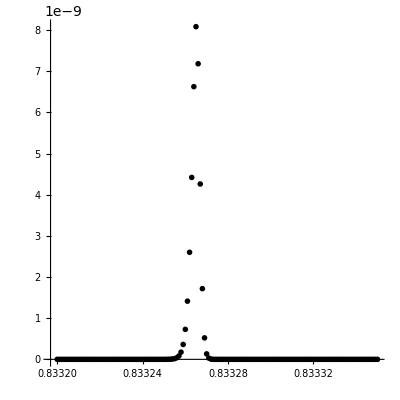

```mathematica
indagine2Plot[3,0.3,10^5,{0.8332,0.83335,10^-6}]
```

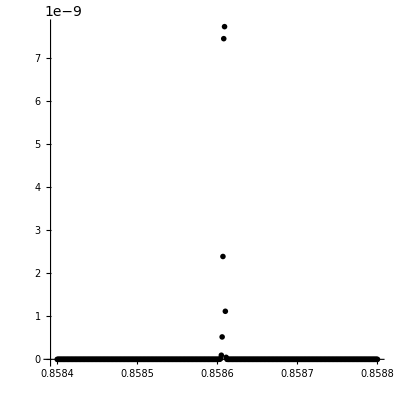

```mathematica
indagine2Plot[4,0.3,10^5,{0.8584,0.8588,10^-6}]
```

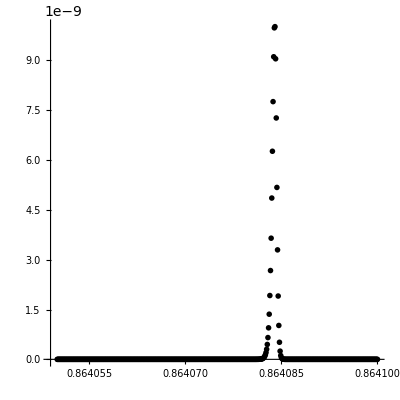

```mathematica
indagine2Plot[5,0.3,10^5,{0.86405,0.8641,10^-7}]
```

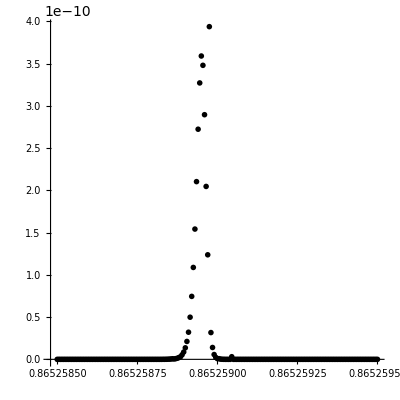

```mathematica
indagine2Plot[6,0.3,10^6,{0.8652585,0.8652595,5*10^-9}]
```

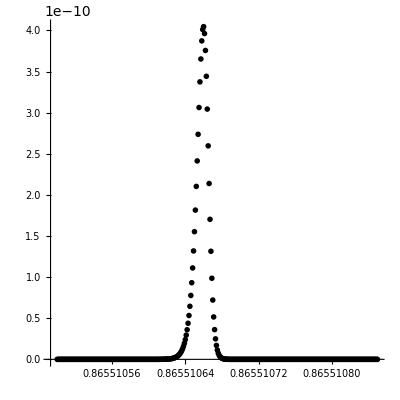

```mathematica
indagine2Plot[7,0.3,10^6,{0.8655105,0.86551085,10^-9}]
```

```mathematica
biforcazioniSin=colpevole2@@@{
{1,0.3,10^4,{0.316,0.32,10^-5}},
{2,0.3,10^5,{0.7196,0.7202,10^-6}},
{3,0.3,10^5,{0.8332,0.83335,10^-6}},
{4,0.3,10^5,{0.8584,0.8588,10^-6}},
{5,0.3,10^5,{0.86405,0.8641,10^-7}},
{6,0.3,10^6,{0.8652585,0.8652595,10^-9}},
{7,0.3,10^6,{0.8655105,0.86551085,10^-9}}
}
```

{0.31828,0.719959,0.833265,0.858609,0.864084,0.865259,0.865511}

```mathematica
rapporti2=Table[(biforcazioniSin⟦n⟧-biforcazioniSin⟦n-1⟧)/(biforcazioniSin⟦n+1⟧-biforcazioniSin⟦n⟧),{n,2,6}]
```

{3.54508,4.47072,4.62904,4.65967,4.66843}